```mathematica
s={r''[t ]-1/(1*(r[t])^3)+1/(r[t])^2(1-0.01/r[t])==0,(r[t])^2*θ'[t]==1}
ics= {r[0]==2+√2,r'[0]==0,θ[0]==0}
sol=NDSolve[{s,ics},{r[t],r'[t],θ[t],θ'[t]},{t,-200,200}]
Plot[Evaluate[r[t]/.sol],{t,-5,50}]

Plot[Evaluate[θ[t]/.sol],{t,-20,200}]
PolarPlot[1/(1+0.9Cos[1.1θ]),{θ,0,50*Pi},PlotRange->Full]
PolarPlot[1/(1+0.9Cos[1.2θ]),{θ,0,50*Pi},PlotRange->Full]
PolarPlot[1/(1+0.9Cos[(1+1/(√7))θ]),{θ,0,100*Pi},PlotRange->Full]
```

{-1/r[t]^3+(1-0.01/r[t])/r[t]^2+r''[t]==0,r[t]^2 θ'[t]==1}

{r[0]==2+√2,r'[0]==0,θ[0]==0}

{{r[t]→InterpolatingFunction[…][t],r'[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],θ'[t]→InterpolatingFunction[…][t]}}

plotting r(t):

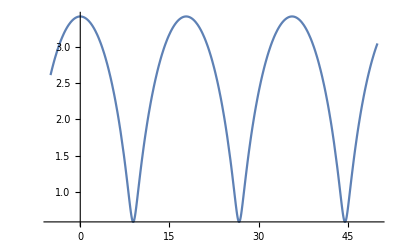

plotting θ(t):

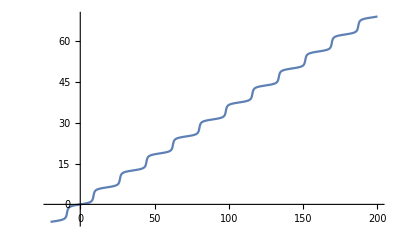

r vs θ polar plotting for Ω = 1.1 :

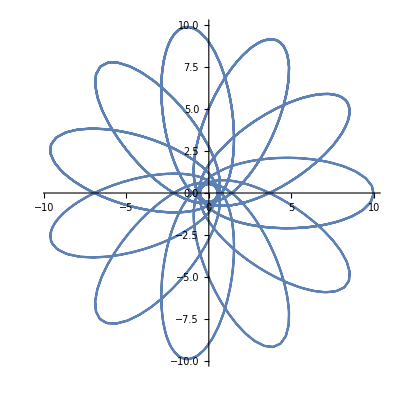

The one that was done analytically in copy: (precession angle: 60^o)

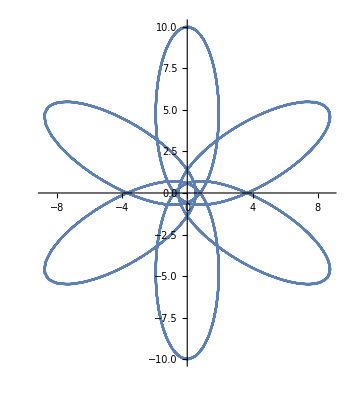

The one for which the orbit is not closed. (Introducing irrationality)